## Define the functions needed for the simulatin

#### Generate randomly split unit intervals

```mathematica
splitIntervals[splitNumber_]:=Module[{one={0,1},two={0,1}},
Do[If[RandomInteger[{1,2}]==1,
AppendTo[one,RandomReal[]],
AppendTo[two,RandomReal[]]],{idx,1,splitNumber}];
one=Sort[one];two=Sort[two];
Return[{one,two}]]
```

#### Find the piece of the other interval that covers a point on this interval

```mathematica
sandwichingSegment[num_,list_]:=Module[{ret={}},Do[If[list[[idx]]<num&&num<list[[idx+1]],ret={list[[idx]],list[[idx+1]]},],{idx,Length[list]-1}];Return[ret]]
```

#### Write the monte carlo that estimates the average

```mathematica
shorterProb[splitNumber_,trialNumber_,separation_]:=Module[{prob={0,0}},
Do[Module[{pair=splitIntervals[splitNumber],one,two,splitIdx},
one=pair[[1]];two=pair[[2]];
splitIdx=RandomInteger[{1,splitNumber}];
If[splitIdx>Length[one]-2,
If[1+splitIdx-(Length[one]-2)+separation<=Length[two],If[sandwichingSegment[two[[1+splitIdx-(Length[one]-2)]],one]==sandwichingSegment[two[[1+splitIdx-(Length[one]-2)+separation]],one],
prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1],
prob[[2]]=prob[[2]]+1],
If[1+splitIdx+separation<=Length[one],If[sandwichingSegment[one[[1+splitIdx]],two]==sandwichingSegment[one[[1+splitIdx+separation]],two],prob[[1]]=prob[[1]]+1,prob[[2]]=prob[[2]]+1],
prob[[2]]=prob[[2]]+1]]],
{trial,trialNumber}];prob=prob/trialNumber*1.;Return[prob]]
```

## Run the simulation

#### Estimate the time taken to run 1000 trials for every separation and every lineage number (or more precisely every split number)

```mathematica
Timing[Table[Table[{recombNum,shorterProb[recombNum,1000,separation][[1]]},{recombNum,50}],{separation,0,6}]][[1]]
```

23.0516

#### Run the full simulation with 50,000 trials for every condition, the estimated time is 25 minutes.

```mathematica
plots=Table[Table[{recombNum,shorterProb[recombNum,50000,separation][[1]]},{recombNum,50}],{separation,0,6}];
```

#### Print the estimated averages to save data (“10” is suppose to be the number of decimal places)

```mathematica
Print[plots]
```

{{{1,1.},{2,1.},{3,1.},{4,1.},{5,1.},{6,1.},{7,1.},{8,1.},{9,1.},{10,1.},{11,1.},{12,1.},{13,1.},{14,1.},{15,1.},{16,1.},{17,1.},{18,1.},{19,1.},{20,1.},{21,1.},{22,1.},{23,1.},{24,1.},{25,1.},{26,1.},{27,1.},{28,1.},{29,1.},{30,1.},{31,1.},{32,1.},{33,1.},{34,1.},{35,1.},{36,1.},{37,1.},{38,1.},{39,1.},{40,1.},{41,1.},{42,1.},{43,1.},{44,1.},{45,1.},{46,1.},{47,1.},{48,1.},{49,1.},{50,1.}},{{1,0.},{2,0.2511},{3,0.33352},{4,0.37582},{5,0.40086},{6,0.41884},{7,0.4273},{8,0.437},{9,0.44166},{10,0.44958},{11,0.45614},{12,0.46284},{13,0.46108},{14,0.46708},{15,0.46624},{16,0.46506},{17,0.47328},{18,0.47146},{19,0.47188},{20,0.47466},{21,0.47008},{22,0.47546},{23,0.47924},{24,0.4796},{25,0.48392},{26,0.47848},{27,0.4851},{28,0.48118},{29,0.4813},{30,0.48362},{31,0.48754},{32,0.48338},{33,0.48082},{34,0.48244},{35,0.4885},{36,0.48152},{37,0.48336},{38,0.49046},{39,0.48542},{40,0.4856},{41,0.48622},{42,0.48824},{43,0.48704},{44,0.4859},{45,0.48956},{46,0.48768},{47,0.49144},{48,0.48962},{49,0.48846},{50,0.4881}},{{1,0.},{2,0.},{3,0.08554},{4,0.12312},{5,0.1518},{6,0.16664},{7,0.1777},{8,0.1903},{9,0.19284},{10,0.19822},{11,0.20208},{12,0.2064},{13,0.2117},{14,0.20992},{15,0.21558},{16,0.21966},{17,0.21922},{18,0.22162},{19,0.22434},{20,0.22342},{21,0.22648},{22,0.22368},{23,0.22706},{24,0.22678},{25,0.2273},{26,0.2293},{27,0.23208},{28,0.23276},{29,0.23172},{30,0.23224},{31,0.22986},{32,0.23328},{33,0.23438},{34,0.23456},{35,0.2367},{36,0.23782},{37,0.23756},{38,0.23366},{39,0.23778},{40,0.23788},{41,0.24072},{42,0.23576},{43,0.23792},{44,0.23598},{45,0.23756},{46,0.23918},{47,0.24098},{48,0.24238},{49,0.24118},{50,0.2374}},{{1,0.},{2,0.},{3,0.},{4,0.03132},{5,0.05066},{6,0.0629},{7,0.07166},{8,0.07858},{9,0.08336},{10,0.08556},{11,0.08992},{12,0.09482},{13,0.09504},{14,0.09942},{15,0.10072},{16,0.10062},{17,0.10344},{18,0.10366},{19,0.10544},{20,0.1068},{21,0.10668},{22,0.1086},{23,0.1082},{24,0.11072},{25,0.1108},{26,0.1113},{27,0.10854},{28,0.11164},{29,0.11112},{30,0.11358},{31,0.11296},{32,0.10994},{33,0.11086},{34,0.11418},{35,0.11362},{36,0.11132},{37,0.11542},{38,0.11608},{39,0.1132},{40,0.11342},{41,0.11822},{42,0.1168},{43,0.11766},{44,0.11656},{45,0.11482},{46,0.11796},{47,0.11666},{48,0.11614},{49,0.11618},{50,0.11568}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.01254},{6,0.02208},{7,0.02698},{8,0.0319},{9,0.03394},{10,0.0374},{11,0.03948},{12,0.04124},{13,0.04202},{14,0.04422},{15,0.04728},{16,0.04846},{17,0.04622},{18,0.04872},{19,0.0492},{20,0.0489},{21,0.04872},{22,0.052},{23,0.05336},{24,0.05232},{25,0.05116},{26,0.05364},{27,0.05446},{28,0.05384},{29,0.0541},{30,0.05542},{31,0.0544},{32,0.0542},{33,0.05608},{34,0.05632},{35,0.05578},{36,0.05558},{37,0.05596},{38,0.05774},{39,0.05642},{40,0.05554},{41,0.05524},{42,0.05492},{43,0.05632},{44,0.05574},{45,0.0573},{46,0.05766},{47,0.05672},{48,0.05764},{49,0.05688},{50,0.05876}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00486},{7,0.00856},{8,0.01164},{9,0.01344},{10,0.01608},{11,0.01686},{12,0.01784},{13,0.01804},{14,0.01984},{15,0.02072},{16,0.0215},{17,0.02294},{18,0.0228},{19,0.0227},{20,0.02306},{21,0.02412},{22,0.02468},{23,0.02462},{24,0.0243},{25,0.02562},{26,0.02528},{27,0.02534},{28,0.0242},{29,0.02482},{30,0.02694},{31,0.02674},{32,0.02664},{33,0.026},{34,0.02734},{35,0.02668},{36,0.02712},{37,0.02722},{38,0.0277},{39,0.0268},{40,0.027},{41,0.02618},{42,0.02736},{43,0.02642},{44,0.02744},{45,0.02772},{46,0.02598},{47,0.0278},{48,0.02806},{49,0.02852},{50,0.02902}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0022},{8,0.00392},{9,0.0054},{10,0.00562},{11,0.00756},{12,0.00824},{13,0.00878},{14,0.00948},{15,0.00966},{16,0.00984},{17,0.00928},{18,0.01078},{19,0.01004},{20,0.01076},{21,0.01116},{22,0.01166},{23,0.01124},{24,0.0117},{25,0.0125},{26,0.01212},{27,0.01166},{28,0.01286},{29,0.01268},{30,0.01126},{31,0.01282},{32,0.01204},{33,0.0126},{34,0.01188},{35,0.01392},{36,0.0136},{37,0.01326},{38,0.01332},{39,0.01282},{40,0.01272},{41,0.01492},{42,0.01368},{43,0.01366},{44,0.01214},{45,0.01252},{46,0.0144},{47,0.01344},{48,0.0135},{49,0.01334},{50,0.0134}}}

## Plot the plots

#### Load the previously printed data if necessary

```mathematica
plots={{{1,1.},{2,1.},{3,1.},{4,1.},{5,1.},{6,1.},{7,1.},{8,1.},{9,1.},{10,1.},{11,1.},{12,1.},{13,1.},{14,1.},{15,1.},{16,1.},{17,1.},{18,1.},{19,1.},{20,1.},{21,1.},{22,1.},{23,1.},{24,1.},{25,1.},{26,1.},{27,1.},{28,1.},{29,1.},{30,1.},{31,1.},{32,1.},{33,1.},{34,1.},{35,1.},{36,1.},{37,1.},{38,1.},{39,1.},{40,1.},{41,1.},{42,1.},{43,1.},{44,1.},{45,1.},{46,1.},{47,1.},{48,1.},{49,1.},{50,1.}},{{1,0.},{2,0.2511},{3,0.33352},{4,0.37582},{5,0.40086},{6,0.41884},{7,0.4273},{8,0.437},{9,0.44166},{10,0.44958},{11,0.45614},{12,0.46284},{13,0.46108},{14,0.46708},{15,0.46624},{16,0.46506},{17,0.47328},{18,0.47146},{19,0.47188},{20,0.47466},{21,0.47008},{22,0.47546},{23,0.47924},{24,0.4796},{25,0.48392},{26,0.47848},{27,0.4851},{28,0.48118},{29,0.4813},{30,0.48362},{31,0.48754},{32,0.48338},{33,0.48082},{34,0.48244},{35,0.4885},{36,0.48152},{37,0.48336},{38,0.49046},{39,0.48542},{40,0.4856},{41,0.48622},{42,0.48824},{43,0.48704},{44,0.4859},{45,0.48956},{46,0.48768},{47,0.49144},{48,0.48962},{49,0.48846},{50,0.4881}},{{1,0.},{2,0.},{3,0.08554},{4,0.12312},{5,0.1518},{6,0.16664},{7,0.1777},{8,0.1903},{9,0.19284},{10,0.19822},{11,0.20208},{12,0.2064},{13,0.2117},{14,0.20992},{15,0.21558},{16,0.21966},{17,0.21922},{18,0.22162},{19,0.22434},{20,0.22342},{21,0.22648},{22,0.22368},{23,0.22706},{24,0.22678},{25,0.2273},{26,0.2293},{27,0.23208},{28,0.23276},{29,0.23172},{30,0.23224},{31,0.22986},{32,0.23328},{33,0.23438},{34,0.23456},{35,0.2367},{36,0.23782},{37,0.23756},{38,0.23366},{39,0.23778},{40,0.23788},{41,0.24072},{42,0.23576},{43,0.23792},{44,0.23598},{45,0.23756},{46,0.23918},{47,0.24098},{48,0.24238},{49,0.24118},{50,0.2374}},{{1,0.},{2,0.},{3,0.},{4,0.03132},{5,0.05066},{6,0.0629},{7,0.07166},{8,0.07858},{9,0.08336},{10,0.08556},{11,0.08992},{12,0.09482},{13,0.09504},{14,0.09942},{15,0.10072},{16,0.10062},{17,0.10344},{18,0.10366},{19,0.10544},{20,0.1068},{21,0.10668},{22,0.1086},{23,0.1082},{24,0.11072},{25,0.1108},{26,0.1113},{27,0.10854},{28,0.11164},{29,0.11112},{30,0.11358},{31,0.11296},{32,0.10994},{33,0.11086},{34,0.11418},{35,0.11362},{36,0.11132},{37,0.11542},{38,0.11608},{39,0.1132},{40,0.11342},{41,0.11822},{42,0.1168},{43,0.11766},{44,0.11656},{45,0.11482},{46,0.11796},{47,0.11666},{48,0.11614},{49,0.11618},{50,0.11568}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.01254},{6,0.02208},{7,0.02698},{8,0.0319},{9,0.03394},{10,0.0374},{11,0.03948},{12,0.04124},{13,0.04202},{14,0.04422},{15,0.04728},{16,0.04846},{17,0.04622},{18,0.04872},{19,0.0492},{20,0.0489},{21,0.04872},{22,0.052},{23,0.05336},{24,0.05232},{25,0.05116},{26,0.05364},{27,0.05446},{28,0.05384},{29,0.0541},{30,0.05542},{31,0.0544},{32,0.0542},{33,0.05608},{34,0.05632},{35,0.05578},{36,0.05558},{37,0.05596},{38,0.05774},{39,0.05642},{40,0.05554},{41,0.05524},{42,0.05492},{43,0.05632},{44,0.05574},{45,0.0573},{46,0.05766},{47,0.05672},{48,0.05764},{49,0.05688},{50,0.05876}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00486},{7,0.00856},{8,0.01164},{9,0.01344},{10,0.01608},{11,0.01686},{12,0.01784},{13,0.01804},{14,0.01984},{15,0.02072},{16,0.0215},{17,0.02294},{18,0.0228},{19,0.0227},{20,0.02306},{21,0.02412},{22,0.02468},{23,0.02462},{24,0.0243},{25,0.02562},{26,0.02528},{27,0.02534},{28,0.0242},{29,0.02482},{30,0.02694},{31,0.02674},{32,0.02664},{33,0.026},{34,0.02734},{35,0.02668},{36,0.02712},{37,0.02722},{38,0.0277},{39,0.0268},{40,0.027},{41,0.02618},{42,0.02736},{43,0.02642},{44,0.02744},{45,0.02772},{46,0.02598},{47,0.0278},{48,0.02806},{49,0.02852},{50,0.02902}},{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0022},{8,0.00392},{9,0.0054},{10,0.00562},{11,0.00756},{12,0.00824},{13,0.00878},{14,0.00948},{15,0.00966},{16,0.00984},{17,0.00928},{18,0.01078},{19,0.01004},{20,0.01076},{21,0.01116},{22,0.01166},{23,0.01124},{24,0.0117},{25,0.0125},{26,0.01212},{27,0.01166},{28,0.01286},{29,0.01268},{30,0.01126},{31,0.01282},{32,0.01204},{33,0.0126},{34,0.01188},{35,0.01392},{36,0.0136},{37,0.01326},{38,0.01332},{39,0.01282},{40,0.01272},{41,0.01492},{42,0.01368},{43,0.01366},{44,0.01214},{45,0.01252},{46,0.0144},{47,0.01344},{48,0.0135},{49,0.01334},{50,0.0134}}};
```

#### Plot the data on a log scale and a (zoomed in) regular scale

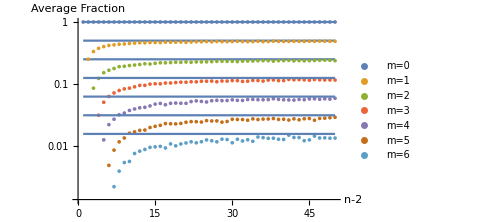
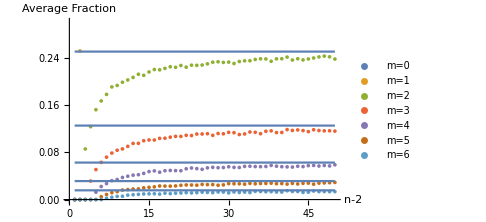

```mathematica
{Show[ListLogPlot[plots,PlotLegends->{"m=0","m=1","m=2","m=3","m=4","m=5","m=6"},AxesLabel->{"n-2","Average Fraction"}],LogPlot[Table[1/2^separation,{separation,0,6}],{recomb,1,50},PlotStyle->Thin],ImageSize->Medium],
Show[ListPlot[plots,PlotLegends->{"m=0","m=1","m=2","m=3","m=4","m=5","m=6"},AxesLabel->{"n-2","Average Fraction"},PlotRange->{0,0.3}],Plot[Table[1/2^separation,{separation,0,6}],{recomb,1,50},PlotStyle->Thin],ImageSize->Medium]}
```

#### Find the percent and absolute errors

```mathematica
errorsPct=Table[Table[{recombNum,(1/2^separation-plots[[separation+1,recombNum,2]])/(1/2^separation)},{recombNum,50}],{separation,0,6}];
errorsAbs=Table[Table[{recombNum,(1/2^separation-plots[[separation+1,recombNum,2]])},{recombNum,50}],{separation,0,6}];
```

#### Plot the percent errors

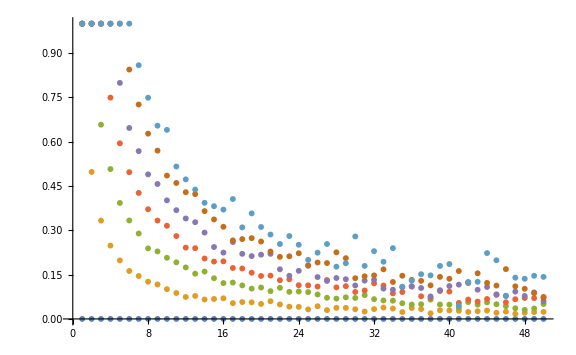

```mathematica
ListPlot[errorsPct,ImageSize->Large]
```

#### Plot the absolute errors on a log scale

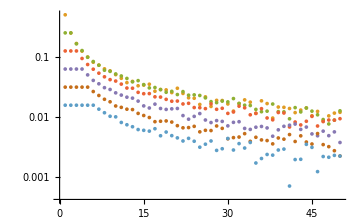

```mathematica
ListLogPlot[errorsAbs,PlotRange->All,ImageSize->Medium]
```

#### Find the accumulative errors (over the first 6 terms)

```mathematica
errorsCum=Table[Total[Transpose[Transpose[errorsAbs][[recombNum]]][[2]]],{recombNum,50}];
```

#### Plot the accumulative errors on a log scale

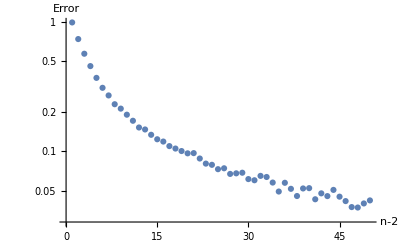

```mathematica
ListLogPlot[errorsCum,PlotRange->All,AxesLabel->{"n-2","Error"}]
```